```mathematica
Dynamic[DrawAll[modalita_]:=Module[{},
SetDirectory[NotebookDirectory[]];
Get["randCard.nb"];
Get["calcolaProb.nb"];
(*
player=Input["Inserisci il numero di giocatori: "];
carteScoperte=Input["Inserisci il numero di carte scoperte: "];
*)
(*
modalita=Input["Inserisci modalità"];
*)
Switch[modalita,1,player=1;carteScoperte=4,
2,player=1;carteScoperte=3,
3,player=1;carteScoperte=3,
4,player=2;carteScoperte=3,
5,player = 3; carteScoperte = 4,
_, "Errore"];

(*CREO LE CARTE DEL BANCO E DEL GIOCATORE*)
{carteBanco,carteGiocatore}=randomCards[carteScoperte,player];

(*CREO IL DISEGNO DELLE CARTE AVVERSARIO*)
Switch[player,
2,
outputavversari=Row[{ImageResize[Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[3]],carteGiocatore[[4]]}],300]}],
3,
outputavversari=Grid[{{Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[3]],carteGiocatore[[4]]},"CardSpreadAngle"->0.4],Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[5]],carteGiocatore[[6]]},"CardSpreadAngle"->0.4]}},Spacings->{Scaled[0.1],Scaled[0.1]},Alignment->Center]
,
_,
"Errore"];


(*CREO IL DISEGNO DELLE CARTE BANCO*)
outputbanco=Row[{ResourceFunction["PlayingCardGraphic"][carteBanco[[1]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[2]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[3]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[4]]],ResourceFunction["PlayingCardGraphic"][carteBanco[[5]]]},Spacer[10]];
outputbanco;

(*CREO IL DISEGNO DELLE CARTE GIOCATORE*)
outputgiocatore=Rasterize@ResourceFunction["PlayingCardGraphic"][{carteGiocatore[[1]],carteGiocatore[[2]]}];
outputgiocatore;


(*DISEGNO LE CARTE*)
(*
If[player>1,Print[outputavversari]];
Print[outputbanco];
Print[outputgiocatore];
*)


(*
Style[Pane[Column[{If[player>1,outputavversari]," ", outputbanco," ",outputgiocatore},Alignment->Center],Alignment->Center,ImageSize->Full],Magnification->1.0]
*)

(*RICAVO LA PROBABILITA' CORRETTA E LA CARTA RICHIESTA*)
{correctprob, requestcard} = calcolaProb[carteBanco, carteGiocatore,player, modalita];

effectivecard = ToString[Mod[requestcard,13]];
Switch[effectivecard,
"11", effectivecard = "J",
"12", effectivecard = "Q",
"13", effectivecard = "K",
_, "Errore"];

(*
Switch[modalita,
1,Print["Qual è la probabilità di fare una coppia di " <>effectivecard<> " estraendo la prossima carta dal mazzo?"],
2, Print["Qual è la probabilità di fare un tris di " <>effectivecard<> " estraendo le prossime 2 carte dal mazzo?"],
3, Print["Qual è la probabilità di fare una coppia di " <>effectivecard<> " estraendo le prossime 2 carte dal mazzo?"],
_, "Errore"]
*)




Return[{outputbanco,outputgiocatore, effectivecard, correctprob}];
]
]
```

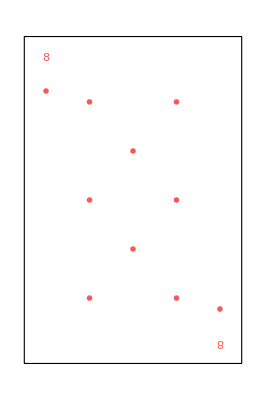
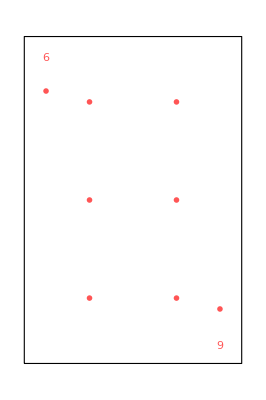
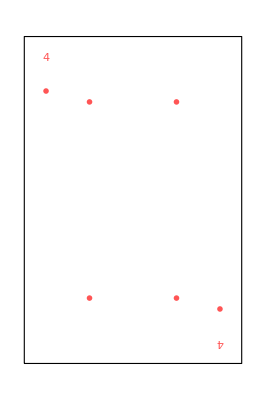
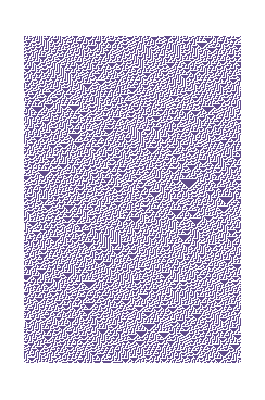
{-Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics-,4,3/46}

```mathematica
DrawAll[1]
```

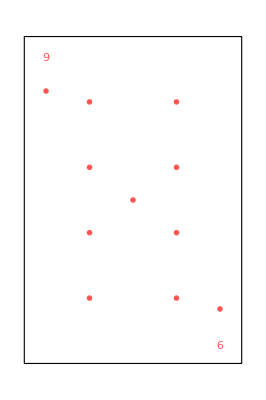
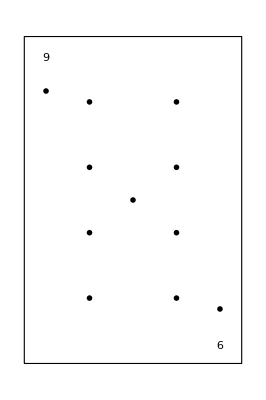
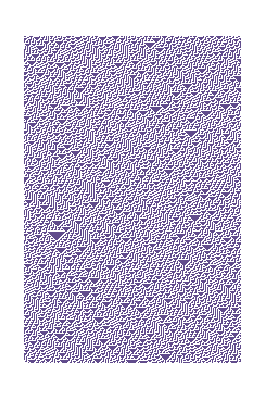
{-Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics-,4,3/46}

```mathematica
DrawAll[1]
```

```mathematica
{{}, {" "}, {}, {" "}}
```